```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

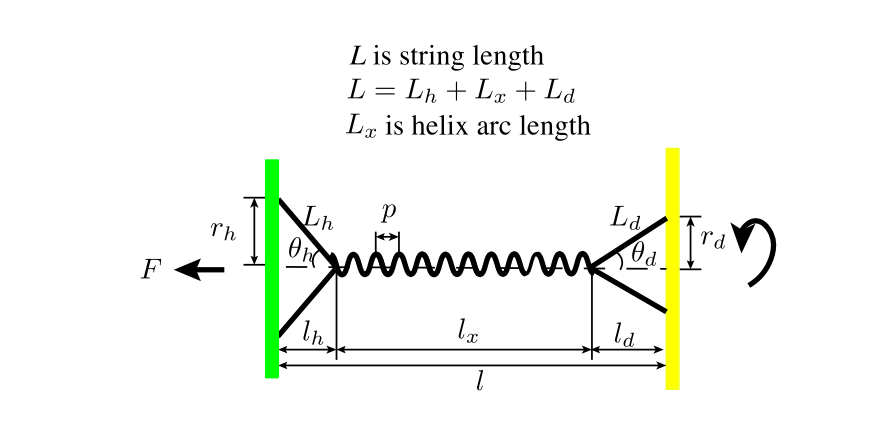
```mathematica
-Graphics-;
```

### Euler-Lagrange equation

U[ϕ(t)] = 2*1/2 E A (Δ(ϕ))^2-2F(t) δ(ϕ(t))
T[ϕ(t)] = 1/2 J ϕ'(t)^2
where J =m_d/2 R_d^2
ℒ =T-U
= 1/2 m_d/2 R_d^2 ϕ'(t)^2+2F(t) δ(ϕ(t))

```mathematica
<<VariationalMethods`
```

```mathematica
EulerEquations[1/2 Subscript[m, d]/2 Subscript[R, d]^2 ϕ'[t]^2+2F[t] (δ[ϕ[t]]),ϕ[t],t];
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

```mathematica
δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)];(*Accurate expression*)
δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2])Subscript[ρ, s])^2);(*approximated expression*)
```

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

General::stop: Further output of Symbolize::bsymbexs will be suppressed during this calculation.

### Comparison with Experiments

#### Set the working directory as the directory where the notebook file is located. The data files are stored in current directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tyler/Documents/BuzzButton/Mathematica

#### Import and extract force F(t) and string length data from files

```mathematica
(*force data*)
rawdata=Import["Data_11.17.20/ForceData.xlsx"];
RawForceData=rawdata[[1, 2;;563,;;2]];
ForceData = RawForceData[[Complement[Range[Length@RawForceData],Flatten@Position[RawForceData[[;;,2]],""]]]];
```

```mathematica
Force= Interpolation[ForceData];
```

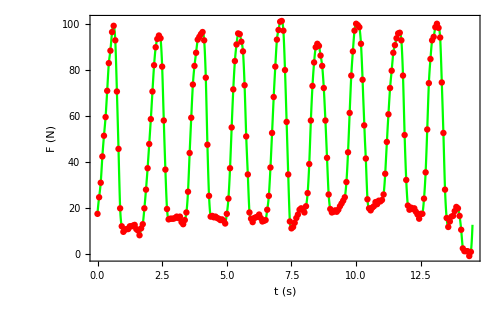

```mathematica
Show[Plot[{Force[t]},{t,0,14.5}
,PlotStyle->{Blue,Green}
,PlotRange->All
,ImageSize->500
,GridLines->None,Axes->False
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["t (s)",Black,FontFamily->"Times",24],Style["F (N)",Black,FontFamily->"Times",24]}
,RotateLabel->True]
,ListPlot[ForceData,PlotStyle->Red]
]
```

```mathematica
(*String length data*)
rawdata=Import["Data_11.17.20/StringLengthData.xlsx"];
```

```mathematica
StringLengthData = rawdata[[1,6;;862,;;2]];
```

```mathematica
SL1 =Interpolation[StringLengthData[[;;,1;;2]]]
```

InterpolatingFunction[…]

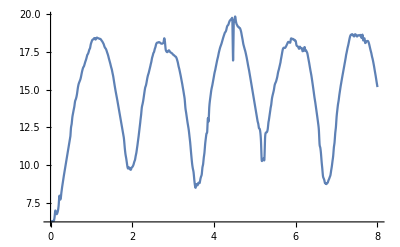

```mathematica
Plot[SL1 [t],{t,0,8}]
```

```mathematica
Manipulate[GraphicsRow[ListLinePlot/@{StringLengthData[[;;,2]],LowpassFilter[StringLengthData[[;;,2]],ω]}],{ω,0.1,20}]
```

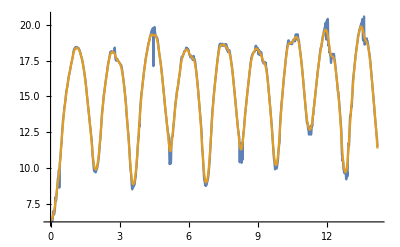

```mathematica
FilterStringLength=Transpose[{StringLengthData[[;;,1]],LowpassFilter[StringLengthData[[;;,2]],0.3]}];
FilterSL1=  Interpolation[FilterStringLength];
Plot[{SL1 [t],FilterSL1 [t]},{t,0,14.2}]
```

#### Prediction of the angular velocity

Symbolize::bsymbexs: Warning: The box structure attempting to be symbolized has a similar or identical symbol already defined, possibly overriding previously symbolized box structure.

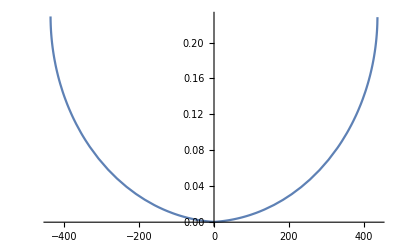

```mathematica
Block[{Subscript[ρ, s]=0.0005
,Subscript[r, h]=0.008
,Subscript[r, d]=0.004
,L=0.23
,Subscript[ϕ, 0]=-2π*48
,Subscript[ω, 0]=0
,J=0.000098
,F
,t1=38.1-6.6},
δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2])Subscript[ρ, s])^2);
Plot[δ[ϕ],{ϕ,-600,600},PlotRange->All]]
```

```mathematica
δd[ϕ1_]:=Piecewise[{{(Subscript[ρ, s] ϕ1 (Subscript[r, d]+Subscript[r, h]+Subscript[ρ, s] √(ϕ1^2)))/(√(ϕ1^2) √(L^2-(Subscript[r, d]+Subscript[r, h]+Subscript[ρ, s] √(ϕ1^2))^2)),(100 Subscript[r, d] Subscript[ρ, s]+100 Subscript[r, h] Subscript[ρ, s]+Subscript[r, d] Subscript[ρ, s]^3+Subscript[r, h] Subscript[ρ, s]^3-10 √(100 L^2 Subscript[ρ, s]^2+L^2 Subscript[ρ, s]^4))/(100 Subscript[ρ, s]^2+Subscript[ρ, s]^4)<ϕ1<(-100 Subscript[r, d] Subscript[ρ, s]-100 Subscript[r, h] Subscript[ρ, s]-Subscript[r, d] Subscript[ρ, s]^3-Subscript[r, h] Subscript[ρ, s]^3+10 √(100 L^2 Subscript[ρ, s]^2+L^2 Subscript[ρ, s]^4))/(100 Subscript[ρ, s]^2+Subscript[ρ, s]^4)},{-10,ϕ1≤(100 Subscript[r, d] Subscript[ρ, s]+100 Subscript[r, h] Subscript[ρ, s]+Subscript[r, d] Subscript[ρ, s]^3+Subscript[r, h] Subscript[ρ, s]^3-10 √(100 L^2 Subscript[ρ, s]^2+L^2 Subscript[ρ, s]^4))/(100 Subscript[ρ, s]^2+Subscript[ρ, s]^4)},{10,ϕ1≥(-100 Subscript[r, d] Subscript[ρ, s]-100 Subscript[r, h] Subscript[ρ, s]-Subscript[r, d] Subscript[ρ, s]^3-Subscript[r, h] Subscript[ρ, s]^3+10 √(100 L^2 Subscript[ρ, s]^2+L^2 Subscript[ρ, s]^4))/(100 Subscript[ρ, s]^2+Subscript[ρ, s]^4)}}];
```

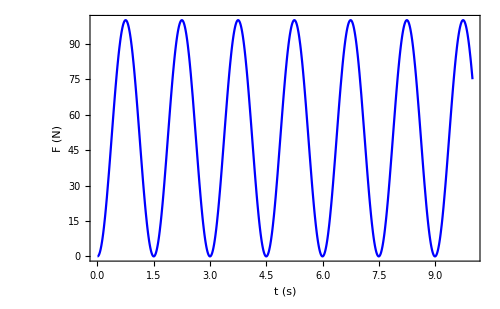

```mathematica
PltForce=Plot[100 Sin[(2π t)/3]^2,{t,0,10},
PlotStyle->{Blue}
,PlotRange->All
,ImageSize->500
,GridLines->None,Axes->False
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["t (s)",Black,FontFamily->"Times",24],Style["F (N)",Black,FontFamily->"Times",24]}
,RotateLabel->True]
```

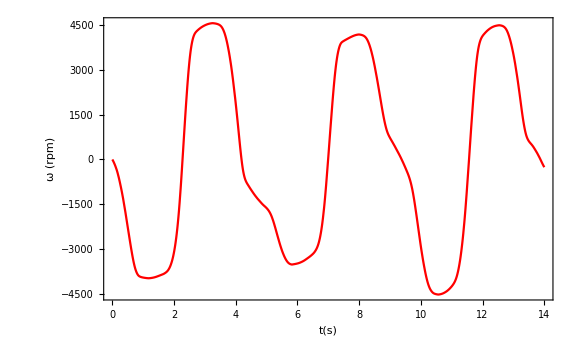

```mathematica
Block[{Subscript[ρ, s]=0.0005
,Subscript[r, h]=0.008
,Subscript[r, d]=0.004
,L=0.23
,Subscript[ϕ, 0]=-2π*48
,Subscript[ω, 0]=0
,J=0.000098
,F
,t1=14},
F[t_]:=-Force[t];(*- 100 Sin[(2π t)/3]^2; -Force[t]*)(* Currently uses actual forcing fn, not fit *)
(*δ[ϕ1_]:=L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2])Subscript[ρ, s])^2);*)
Sol=NDSolve[{J ϕ''[t]==2F[t]* (δd[ϕ[t]]),ϕ[0]==Subscript[ϕ, 0],ϕ'[0]==Subscript[ω, 0]},ϕ,{t,0,t1}];
Pred=Plot[
{-60/(2π)Evaluate[ϕ'[t]/.Sol[[1]]]}
,{t,0,t1}
,PlotStyle->{Red}
,ImageSize->Large
,PlotRange->All
,GridLines->None,Axes->False,AxesStyle->Directive[Black,FontFamily->"Times",24]
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20]
,FrameLabel->{Style["t(s)",Black,FontFamily->"Times",24],Style["ω (rpm)",Black,FontFamily->"Times",24]}
,RotateLabel->False]
]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tyler/Documents/BuzzButton/Mathematica

```mathematica
Export["Data_11.17.20/PltForce.pdf",PltForce]
Export["Data_11.17.20/PltAngularV.pdf",Pred]
```

Data_11.17.20/PltForce.pdf

Data_11.17.20/PltAngularV.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Data_11.17.20/PltForce.pdf"]]]
```

#### Import and extract angular velocity ω(t) data from files

```mathematica
rawdata=Import["Data_11.17.20/ButtonSpeedData.xlsx"];
RawAVData=rawdata[[1,2;;, 1;;2]];(*The unit is rpm *)
Pos=Flatten@Position[RawAVData[[;;,2]],x_/;Abs[x]>0.0001];
AVData= RawAVData[[Pos]];
```

```mathematica
(*This line deals with zero off-set, in case button speed doesn't immediately start increasing *)
(*AVData1= {AVData[[330;;,1]]-AVData[[330,1]],AVData[[330;;,2]]}^ᵀ;*)
```

```mathematica
(*AVData[[330]]*)
```

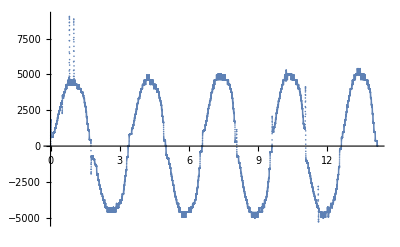

```mathematica
Mesu=ListPlot[AVData]
```

```mathematica
Show[ForcePlot,Mesu] (*not sure why this stopped working*)
```

Show::gcomb: Could not combine the graphics objects in Show[ForcePlot,].

Show[ForcePlot,-Graphics-]

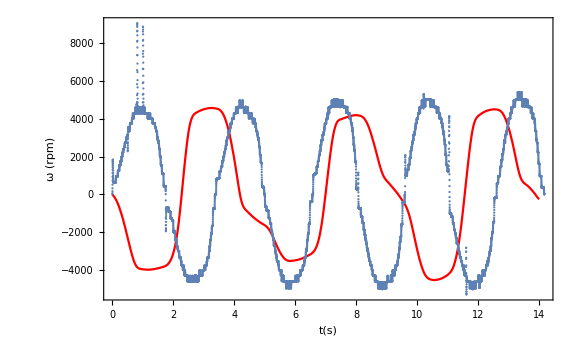

```mathematica
Show[Pred,Mesu]
```

#### Extract String Length Data

```mathematica
rawdata=Import["Data_11.17.20/StringLengthData.xlsx"];
Dispdata = rawdata[[1,6;;862,;;2]];
Disp = Interpolation[Dispdata[[;;,1;;2]]];(*The unit is cm/s *)
```

#### Plot the displacement data

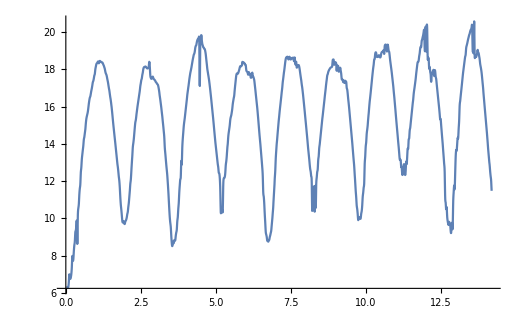

```mathematica
Plot[Disp[t],{t,0,14.2}]
```

#### Plot and check the displacement-rotation relation

InterpolatingFunction::dmval: Input value {14.2871} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {15.7157} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {17.1443} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

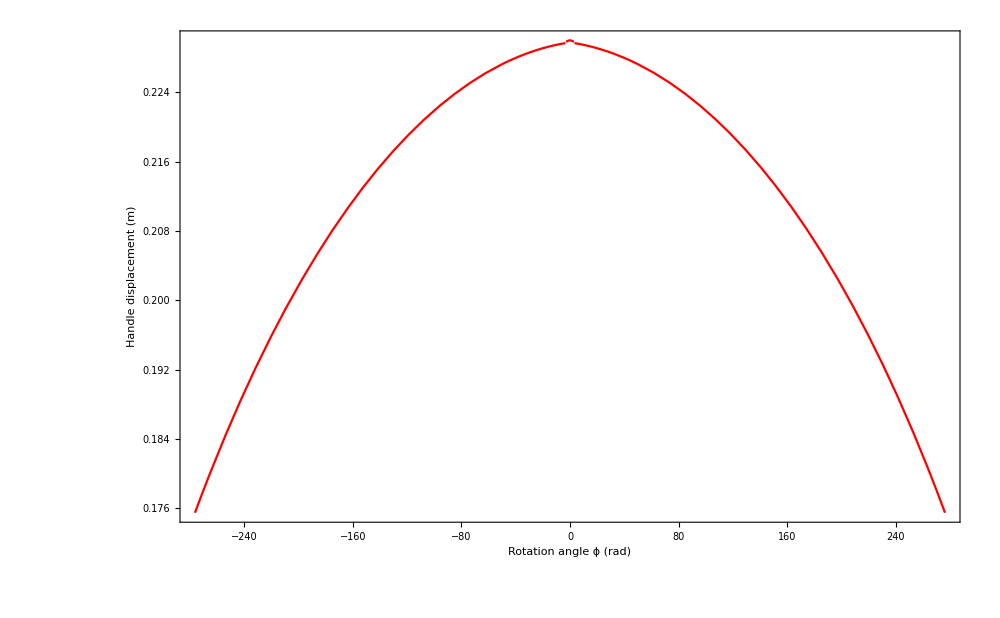

```mathematica
Block[{Subscript[ρ, s]=0.0005
,Subscript[r, h]=0.008
,Subscript[r, d]=0.004
,L=0.23
,x},
δ[ϕ1_]:=Piecewise[{{L-Sqrt[L^2-2 Subscript[r, d]^2+2 Subscript[r, d]^2 Cos[ϕ1]],-π<ϕ1<π}},L-√(L^2-(Subscript[r, d]+Subscript[r, h]+(Sqrt[ϕ1^2]-π)Subscript[ρ, s])^2)];
Show[
Plot[L-δ[ϕ],{ϕ,-44*2π,44*2π}
,PlotStyle->{Red}
,PlotRange->All
,ImageSize->1000
,GridLines->None,Axes->False
,Frame->True,FrameStyle->Directive[FontFamily->"Times",20],FrameLabel->{Style["Rotation angle ϕ (rad)",Black,FontFamily->"Times",24],Style["Handle displacement (m)",Black,FontFamily->"Times",24]}
,RotateLabel->True],
ParametricPlot[{ 2π Turns[t],Disp[t]/100},{t,0,70},PlotStyle->Blue,AspectRatio->1]
]
]
```